```mathematica
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"CMU serif",FontSize->12};
stil[t_]:=Style[t,{Black,FontSize->20}]
genplot[phi_]:=Module[{},hs=Range[0.2,1.8,0.2];
examples=Table[phi[Abs[r],h],{h,hs}];
colors=Table[Blend[{Red,Blue},i/(Length[hs]-1)],{i,0,Length[hs]-1}];
Plot[Evaluate@examples,{r,-2,2},
BaseStyle->texStyle,
PlotStyle->colors,
Frame->True,
Axes->False,
FrameLabel->{MaTeX["r",Magnification->1.2],MaTeX["\\psi(r)",Magnification->1.2]},
GridLines->Automatic,
PlotRange->All,
ImageSize->Medium,
PlotLegends->LineLegend[colors,hs,LegendLabel->MaTeX["\\sigma_b",Magnification->1.5],LabelStyle->texStyle],
FrameStyle->Black
]
]
```

```mathematica
genplot[phi2]
```

-Graphics-

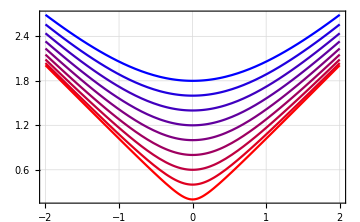
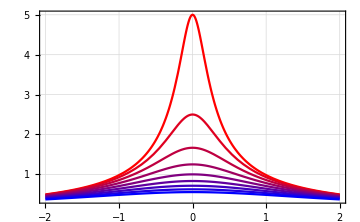
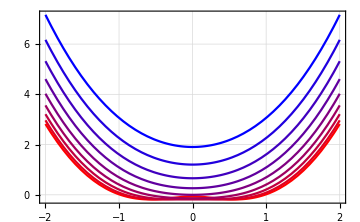
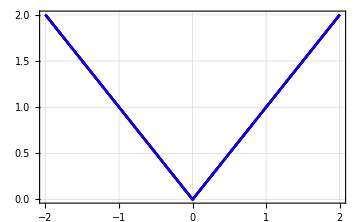
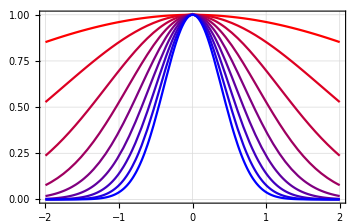

```mathematica
phi1[r_,h_]:=Sqrt[r^2+h^2]
phi2[r_,h_]:=1/Sqrt[r^2+h^2]
phi3[r_,h_]:=(r^2+h^2)Log@Sqrt[r^2+h^2]
phi4[r_,h_]:=r
phi5[r_,h_]:=Exp[-h^2r^2]
fns={phi1, phi2, phi3, phi4, phi5};
plots=Map[genplot,fns];
plots[[4]]=plots[[4]]/.Legended[p_,r__]->p;
plots
```

```mathematica
Export["../images/rbf_mq.pdf",plots[[1]]];
Export["../images/rbf_imq.pdf",plots[[2]]];
Export["../images/rbf_tps.pdf",plots[[3]]];
Export["../images/rbf_lin.pdf",plots[[4]]];
Export["../images/rbf_gau.pdf",plots[[5]]];
```